1. Using Around, or otherwise, plot a graph of the points (0.0, 0.19 .06 .01),
(1.0, 0.76 .06 0.1), (2.0, 5.4 .06 0.5), (3.0, 9.0 .06 1), (4.0, 25. .06 2) and
(5.0, 76 .06 3), and superpose a plot of sinh(x) for 0 < x < 5. Ensure that
the whole graph, including all the error bars, is visible. [7]

{{0.,0.1900.010},{1.,0.760.10},{2.,5.40.5},{3.,9.01.0},{4.,25.02.0},{5.,76.03.0}}

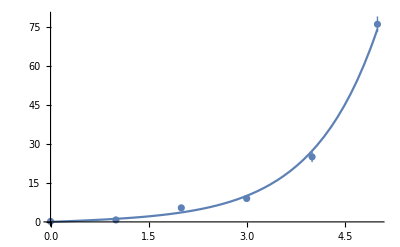

```mathematica
plots = {{0.0,Around[0.19,0.01]},{1.0, Around[0.76,0.1]}, {2.0,Around[5.4,0.5]}, {3.0,Around[9.0,1]},{4.0,Around[25,2]},{5.0,Around[76,3]}}
Show[ListPlot[plots],
Plot[Sinh[x],{x,0,5}]
]
```

2. Find the values of a, b and c which provide the best fit of a + bx + cx2 to
cos(x) over the range 0 < x < .19=2 by integrating
􀀀
a + bx + cx2 􀀀 cos(x)
.012 over the required range and using
FindMinimum to find the optimal values of a, b and c. Also give the
result of expanding cos(x) about x = 0 up to the term in x2 using
Series. [7]

```mathematica
q2integral=Integrate[(a+b x+c x^2-Cos[x])^2,{x,0,π/2}]
FindMinimum[q2integral==0,a]
seriesCosx=Series[Cos[x],{x,0,3}]
```

-2 a+2 b+1/4 (1+2 a^2) π-b π+1/4 a b π^2+1/24 (b^2+2 a c) π^3+1/32 b c π^4+(c^2 π^5)/160-1/2 c (-8+π^2)

FindMinimum::nrnum: The function value 0.356194+4.4674 b-b π+1/24 (b^2+2. c) π^3+1/32 b c π^4+(c^2 π^5)/160-1/2 c (-8+π^2)==0 is not a real number at {a} = {1.}.

FindMinimum[q2integral==0,a]

1-x^2/2+O[x]^4

3. Use ElementData[n,”AbsoluteMeltingPoint”] to construct a
list of ordered pairs felement number, melting pointg for all the
elements from 1 to 92. Plot the associated points, labelling the axes
appropriately. You should see no consistent pattern, as the bonding
between the atoms varies in character from column to column in the
Periodic Table.
By using ElementData[n,”Series”] generate another table of the
form fseries, element number, melting pointg, select the elements from
the series “AlkaliMetal”, and generate a line plot of their melting
points as a function of atomic number. You may find Select, Map and
Rest useful. [7]

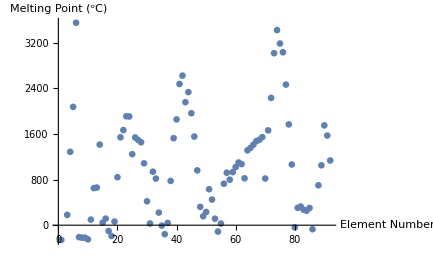

```mathematica
elements=Table[{n,ElementData[n,"MeltingPoint"]},{n,1,92}];
ListPlot[elements, AxesLabel->{"Element Number","Melting Point (^oC)"}]
```

```mathematica
elementseries=Table[{ElementData[n,"Series"],n,ElementData[n,"MeltingPoint"]},{n,1,92}];
```

4. Nonlinear differential equations are usually not analytically soluble, but
there are exceptions such as the separable equation dx=dt = sin(x).
Solve this equation analytically for the initial conditions x(0) = 0,
x(0) = 1=2 and x(0) = 1, and plot all three solutions on the same graph,
with appropriate legends. [6]

x'[t]==Sin[x[t]]

{0}

{2 ArcCot[ⅇ^-t Cot[1/4]]}

{2 ArcCot[ⅇ^-t Cot[1/2]]}

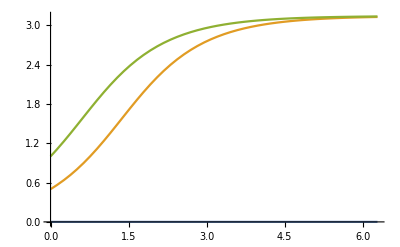

```mathematica
q4Diff = D[x[t],t]==Sin[x[t]]
dSolver[y_]:=DSolve[{q4Diff,x[0]==y},x[t],t]
x1[t_]=x[t]/.dSolver[0]
x2[t_]=x[t]/.dSolver[1/2]
x3[t_]=x[t]/.dSolver[1]
Plot[{x1[t],x2[t],x3[t]}, {t,0,2π}]
```

5.

```mathematica
a1={a11,a12,a13}
a2={a21,a22,a23}
a3={a31,a32,a33}
b1 = Cross[a2,a3/(Dot[a1,Cross[a2,a3]])];
b2 = Cross[a3,a2/(Dot[a3,Cross[a1,a2]])];
b3=Cross[a2,a3/(Dot[a2,Cross[a3,a1]])];
a1Dotb1=Simplify[Dot[a1,b1]]
a1Dotb2 = Simplify[Dot[a1,b2]]
a1Dotb3= Simplify[Dot[a1,b3]]
```

{a11,a12,a13}

{a21,a22,a23}

{a31,a32,a33}

1

-1

1

6. Write a function which will accept one argument and which has the
following properties:
(a) it will return “Error” if the argument is not an integer between
1000 and 9999 inclusive
(b) it will return “Correct” if the last digit is equal to the sum of the
first three digits modulo 10;
(c) it will return “CheckSum Failed” otherwise.
Check that your function works correctly (this will require at least 3
checks). You may find the IntegerDigits, Most and Mod functions
useful. [7]

```mathematica
checksum[x_Integer]:=Module[{digits=IntegerDigits[x]},
sum = Mod[digits[[1]]+digits[[2]]+digits[[3]] ,10];
sum==digits[[4]]
]
checksum[1002]
```

False

```mathematica
integerFunction[x_]:= If[
(1000<x<9999),If[checksum[x],"Correct","CheckSum Failed"],"Error"]
```

7.